```mathematica
dataI=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/326/I.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]]
```

{{N,R, kOm,x, cm,\sigma_x,I, A 10^-8,\sigma_I},{1.,20.,21.6,0.2,9.92,0.1},{2.,23.,19.,0.2,8.66,0.09},{3.,26.,16.7,0.2,7.68,0.08},{4.,29.,15.1,0.2,6.9,0.07},{5.,32.,13.8,0.2,6.27,0.06},{6.,35.,12.6,0.2,5.74,0.06},{7.,38.,11.6,0.2,5.29,0.05},{8.,41.,10.8,0.2,4.91,0.05},{9.,45.,9.9,0.2,4.48,0.04},{10.,50.,9.,0.2,4.03,0.04},{11.,60.,7.6,0.2,3.37,0.03},{12.,70.,6.5,0.2,2.89,0.03}}

```mathematica
dataI//TableForm
```

N | R, kOm | x, cm | \sigma_x | I, A 10^-8 | \sigma_I
1. | 20. | 21.6 | 0.2 | 9.92 | 0.1
2. | 23. | 19. | 0.2 | 8.66 | 0.09
3. | 26. | 16.7 | 0.2 | 7.68 | 0.08
4. | 29. | 15.1 | 0.2 | 6.9 | 0.07
5. | 32. | 13.8 | 0.2 | 6.27 | 0.06
6. | 35. | 12.6 | 0.2 | 5.74 | 0.06
7. | 38. | 11.6 | 0.2 | 5.29 | 0.05
8. | 41. | 10.8 | 0.2 | 4.91 | 0.05
9. | 45. | 9.9 | 0.2 | 4.48 | 0.04
10. | 50. | 9. | 0.2 | 4.03 | 0.04
11. | 60. | 7.6 | 0.2 | 3.37 | 0.03
12. | 70. | 6.5 | 0.2 | 2.89 | 0.03

```mathematica
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
```

```mathematica
Needs@"ErrorBarPlots`";
vertSize=0.01;horizSize=0.03;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
myTicksX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,2}]
myTicksY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,1}]
```

```mathematica
forFit=(*Select[*)dataI⟦2;;,{3,5}⟧(*,First@#>22&]*);
fit=LinearModelFit[forFit(*⟦All,;;2⟧*),{x,1},x];
forFit
fit@"ParameterTable"
fit@"Function"
```

{{21.6,9.92},{19.,8.66},{16.7,7.68},{15.1,6.9},{13.8,6.27},{12.6,5.74},{11.6,5.29},{10.8,4.91},{9.9,4.48},{9.,4.03},{7.6,3.37},{6.5,2.89}}

| Estimate | Standard Error | t-Statistic | P-Value
x | 0.465643 | 0.00176697 | 263.526 | 1.52259×10^-20
1 | -0.138508 | 0.0240003 | -5.77109 | 0.000179909

-0.138508+0.465643 #1&

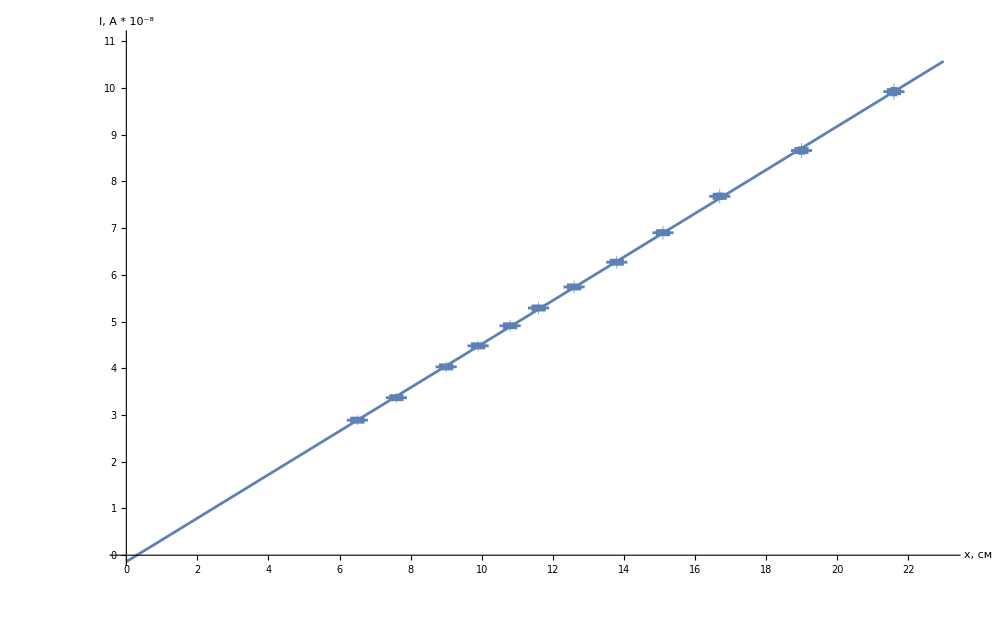

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataI⟦2;;,{3,5,4,6}⟧,
GridLines->{grids@1,grids@0.5},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"x, см","I, A * 10^-8"},
AxesStyle->Directive[Large,Black],
ErrorBarFunction->Function[{coords,errors},{Thickness@0.005,vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)}],
PlotMarkers->{Automatic,0.01},Joined->False,PlotStyle->Thickness@0.3,
PlotRange->{{0.00000,23},{0.0000000,10.9999}},Ticks->{myTicksX, myTicksY},
ImageSize->1000],Plot[fit["Function"]@x,{x,0,23}, PlotStyle->Thickness@0.002]]
```

```mathematica
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
forTeXC=MapAt[dropLastDot@*ToString,dataI,{{2;;,All}}];
forTeXC//TeXForm
```

\left(
\begin{array}{cccccc}
 \text{N} & \text{R, kOm} & \text{x, cm} & \text{$\backslash \backslash $sigma$\_$x} & \text{I, A 10${}^{\wedge}$-8} & \text{$\backslash \backslash
   $sigma$\_$I} \\
 1 & 20 & 21.6 & 0.2 & 9.92 & 0.1 \\
 2 & 23 & 19 & 0.2 & 8.66 & 0.09 \\
 3 & 26 & 16.7 & 0.2 & 7.68 & 0.08 \\
 4 & 29 & 15.1 & 0.2 & 6.9 & 0.07 \\
 5 & 32 & 13.8 & 0.2 & 6.27 & 0.06 \\
 6 & 35 & 12.6 & 0.2 & 5.74 & 0.06 \\
 7 & 38 & 11.6 & 0.2 & 5.29 & 0.05 \\
 8 & 41 & 10.8 & 0.2 & 4.91 & 0.05 \\
 9 & 45 & 9.9 & 0.2 & 4.48 & 0.04 \\
 10 & 50 & 9 & 0.2 & 4.03 & 0.04 \\
 11 & 60 & 7.6 & 0.2 & 3.37 & 0.03 \\
 12 & 70 & 6.5 & 0.2 & 2.89 & 0.03 \\
\end{array}
\right)

```mathematica
dataL=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/326/L.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
```

```mathematica
dataL//TableForm
```

N | R, kOm | 1/R+r_0, 10^-6 | L | Sigma L
1. | 50. | 19.8 | 21.4 | 0.3
2. | 45. | 21.9 | 20.3 | 0.3
3. | 40. | 24.7 | 19.6 | 0.3
4. | 30. | 32.7 | 18.4 | 0.3
5. | 20. | 48.6 | 16.6 | 0.3
6. | 15. | 64.3 | 15.2 | 0.3
7. | 10. | 94.7 | 13.2 | 0.3
8. | 8. | 116.8 | 12. | 0.3
9. | 6. | 152.4 | 10.4 | 0.3
10. | 4. | 219.3 | 8.6 | 0.3
11. | 3. | 280.9 | 7.4 | 0.3
12. | 2.5 | 326.8 | 7. | 0.3

```mathematica
forTeXL=MapAt[dropLastDot@*ToString,dataL,{{2;;,All}}];
forTeXL//TeXForm
```

\left(
\begin{array}{ccccc}
 \text{N} & \text{R, kOm} & \text{1/R+r$\_$0, 10${}^{\wedge}$-6} & \text{L} & \text{Sigma L} \\
 1 & 50 & 19.8 & 21.4 & 0.3 \\
 2 & 45 & 21.9 & 20.3 & 0.3 \\
 3 & 40 & 24.7 & 19.6 & 0.3 \\
 4 & 30 & 32.7 & 18.4 & 0.3 \\
 5 & 20 & 48.6 & 16.6 & 0.3 \\
 6 & 15 & 64.3 & 15.2 & 0.3 \\
 7 & 10 & 94.7 & 13.2 & 0.3 \\
 8 & 8 & 116.8 & 12 & 0.3 \\
 9 & 6 & 152.4 & 10.4 & 0.3 \\
 10 & 4 & 219.3 & 8.6 & 0.3 \\
 11 & 3 & 280.9 & 7.4 & 0.3 \\
 12 & 2.5 & 326.8 & 7 & 0.3 \\
\end{array}
\right)

```mathematica
forTeXR=MapAt[dropLastDot@*ToString,dataR,{{2;;,All}}];
forTeXR//TeXForm
```

\left(
\begin{array}{cccccc}
 \text{N} & \text{R, kOm} & \text{x$\_$n} & \text{x$\_$n+k} & \text{Theta} & \text{R $\unicode{043a}\unicode{0440}$} \\
 1 & 24 & 5.9 & 0.8 & 2 & 6.89 \\
 2 & 28 & 11.1 & 1.7 & 1.88 & 7.62 \\
 3 & 32 & 10.6 & 1.6 & 1.67 & 7.81 \\
 4 & 36 & 10.3 & 2.4 & 1.46 & 7.7 \\
 5 & 40 & 10.2 & 2.7 & 1.33 & 7.84 \\
 6 & 44 & 9.8 & 3 & 1.18 & 7.69 \\
 7 & 48 & 9.8 & 3.2 & 1.12 & 7.96 \\
 8 & 56 & 14.4 & 5.3 & 1 & 8.33 \\
 9 & 64 & 13 & 5.2 & 0.92 & 8.76 \\
 10 & 72 & 12 & 5.2 & 0.84 & 9.02 \\
 11 & 80 & 11.8 & 5.5 & 0.76 & 9.16 \\
\end{array}
\right)

```mathematica
dataR=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/326/R.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataR//TableForm
dataR//TeXForm
```

N | R, kOm | x_n | x_n+k | Theta  | R кр
1. | 24. | 5.9 | 0.8 | 2. | 6.89
2. | 28. | 11.1 | 1.7 | 1.88 | 7.62
3. | 32. | 10.6 | 1.6 | 1.67 | 7.81
4. | 36. | 10.3 | 2.4 | 1.46 | 7.7
5. | 40. | 10.2 | 2.7 | 1.33 | 7.84
6. | 44. | 9.8 | 3. | 1.18 | 7.69
7. | 48. | 9.8 | 3.2 | 1.12 | 7.96
8. | 56. | 14.4 | 5.3 | 1. | 8.33
9. | 64. | 13. | 5.2 | 0.92 | 8.76
10. | 72. | 12. | 5.2 | 0.84 | 9.02
11. | 80. | 11.8 | 5.5 | 0.76 | 9.16

\left(
\begin{array}{cccccc}
 \text{N} & \text{R, kOm} & \text{x$\_$n} & \text{x$\_$n+k} & \text{Theta} & \text{R $\unicode{043a}\unicode{0440}$} \\
 1. & 24. & 5.9 & 0.8 & 2. & 6.89 \\
 2. & 28. & 11.1 & 1.7 & 1.88 & 7.62 \\
 3. & 32. & 10.6 & 1.6 & 1.67 & 7.81 \\
 4. & 36. & 10.3 & 2.4 & 1.46 & 7.7 \\
 5. & 40. & 10.2 & 2.7 & 1.33 & 7.84 \\
 6. & 44. & 9.8 & 3. & 1.18 & 7.69 \\
 7. & 48. & 9.8 & 3.2 & 1.12 & 7.96 \\
 8. & 56. & 14.4 & 5.3 & 1. & 8.33 \\
 9. & 64. & 13. & 5.2 & 0.92 & 8.76 \\
 10. & 72. & 12. & 5.2 & 0.84 & 9.02 \\
 11. & 80. & 11.8 & 5.5 & 0.76 & 9.16 \\
\end{array}
\right)

```mathematica
forFit=(*Select[*)dataGr⟦2;;,{3,1}⟧(*,First@#>22&]*);
fit=LinearModelFit[forFit(*⟦All,;;2⟧*),{x,1},x];
forFit
fit@"ParameterTable"
fit@"Function"
```

{{0.77,6.21},{0.48,3.47},{0.29,2.41},{0.2,1.69},{0.15,1.01},{0.13,0.89},{0.09,0.77},{0.08,0.62}}

```mathematica
{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {x, 7.957906853747322, 0.28153265746757256, 28.26637209810705, 1.2976379087486643*^-7}, {1, -0.044727001213329225, 0.09960150353354393, -0.4490594983665684, 0.6691529353975434}}
```

| Estimate | Standard Error | t-Statistic | P-Value
x | 7.95791 | 0.281533 | 28.2664 | 1.29764×10^-7
1 | -0.044727 | 0.0996015 | -0.449059 | 0.669153

```mathematica
myTicksXL[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,50}]
myTicksYL[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,3}]
```

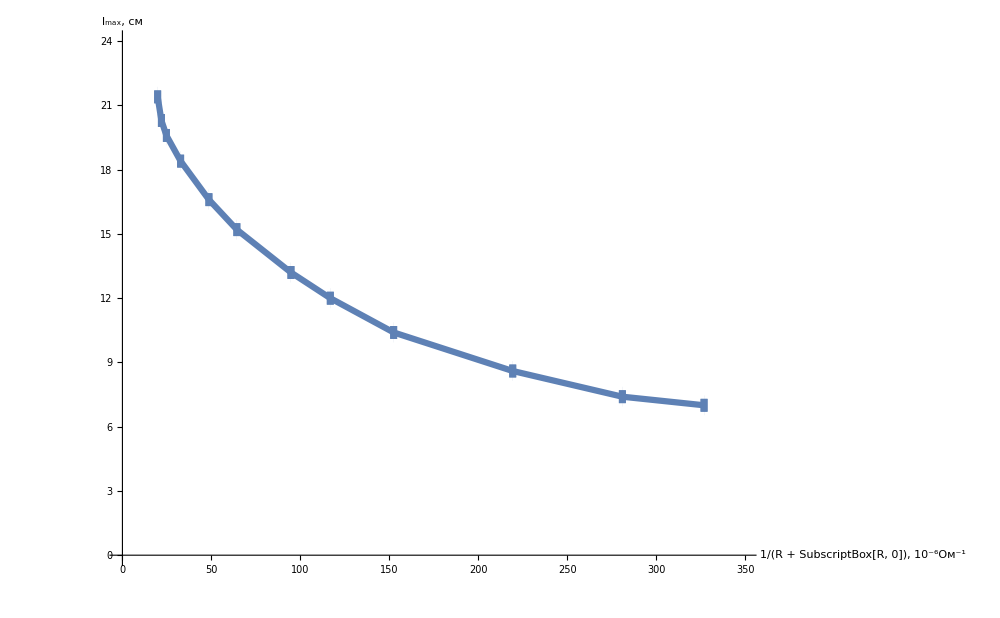

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataL⟦2;;,{3,4,5,5}⟧,
GridLines->{grids@25,grids@1},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"1/(R + SubscriptBox[R, 0]), 10^-6(:041e:043c)^-1","l_max, см"},
AxesStyle->Directive[Large,Black],
ErrorBarFunction->Function[{coords,errors},{Thickness@0.005,vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),(*horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)*)}],
PlotMarkers->{Automatic,0.01},Joined->True,PlotStyle->Thickness@0.0045,
PlotRange->{{0, 349},{0,24}},(*Ticks->{myTicksXL, myTicksYL},*)
ImageSize->1000](*,Plot[fit["Function"]@x,{x,0,4.5}, PlotStyle->Thickness@0.005]*)]
```